# Log-Log Plots

```mathematica
(* Since Mathematica operates in a global environment, let's clear all that, so we're clean *)
Clear["Global`"];
(* Buttons to hide / show code *)
CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

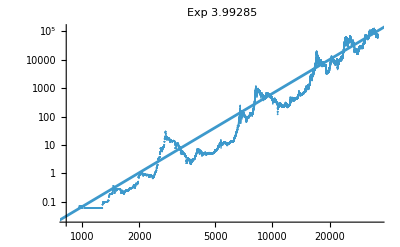

```mathematica
prices=URLExecute["http://localhost:3110/api/v1/historical-price"];
vals=Drop[
Lookup[Values[prices][[1]],"USD"]
,2500
];
(*fit=FindFit[vals,a*x^b,{a,b},x];*)
fit=FindFit[vals,a*x^b,{a,b},x,MaxIterations->200];
fitFn=Function[x,Evaluate[a*x^b/. fit]];
Show[
ListLogLogPlot[vals, PlotLabel->StringForm["Exp ``",b/.fit] ]
,LogLogPlot[fitFn[x],{x,Min[vals],Max[vals]}]
]
```

```mathematica
nlm=NonlinearModelFit[vals,a*x^b,{a,b},x,MaxIterations->500];
nlm["RSquared"]
(*std errors,t-stats, p-values*)
nlm["ParameterTable"]
```

0.899245

General::munfl: Exp[-40932.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.16597×10^6] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | 6.96391×10^-14 | 1.23431×10^-16 | 564.193 | 0.
b | 3.99285 | 8.9143×10^-29 | 4.47915×10^28 | 0.

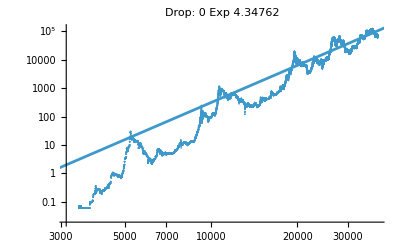
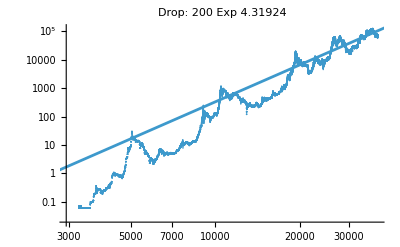
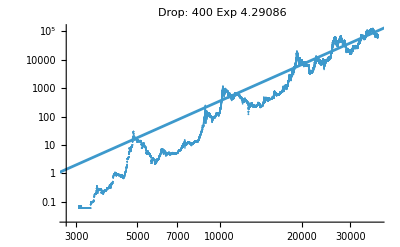
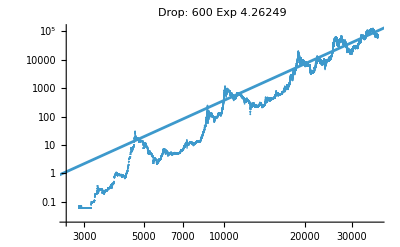
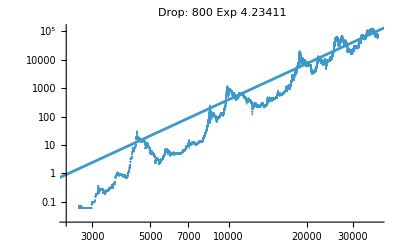
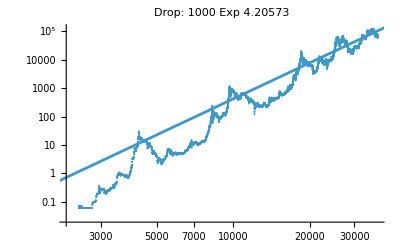
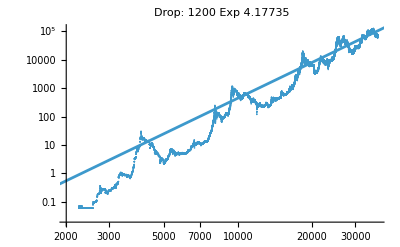
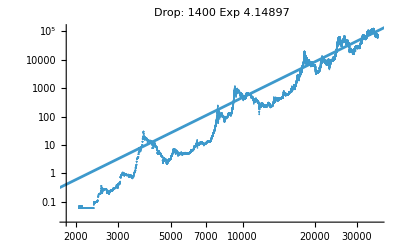

```mathematica
Table[
vals=Drop[
Lookup[Values[prices][[1]],"USD"]
,d
];
(*fit=FindFit[vals,a*x^b,{a,b},x];*)
fit=FindFit[vals,a*x^b,{{a},{b}},x,MaxIterations->1000];
fitFn=Function[x,Evaluate[a*x^b/. fit]];
Show[
ListLogLogPlot[vals, PlotLabel->StringForm["Drop: `` Exp ``",d,b/.fit] ]
,LogLogPlot[fitFn[x],{x,Min[vals],Max[vals]}]
]
,{d,0,3000,200}
]
```

```mathematica
b/. fit
```

3.92188

```mathematica
b/.fit
```

3.92188

```mathematica
StringForm
```

```mathematica
fitFn/@vals
```